## I don't know why I need the factor of √3 in these to get agreement--probably because you need to draw temperature T from a MB distr!!!

## numbers chosen to match fig. 2b)i) of http://arxiv.org/pdf/0805.3510.pdf

```mathematica
MaxwellDistribution
```

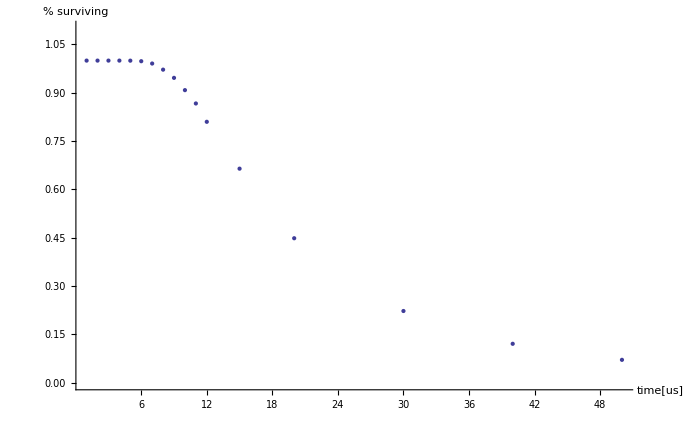

```mathematica
Clear["Global`*"]
nSim=10000;(*number of random atoms*)


g=9.81;

kB = 1.38 10^-23;

T=50 10^-6; (*temp of atom in tweezer*)

Ttr=1.2 10^-3;

m=2.21 10^-25;

fax=20 10^3;
frad=85 10^3;
(*
T=168 10^-6; (*temp of atom in tweezer*)

Ttr=2.8 10^-3;

m=1.44 10^-25;

fax=30 10^3;
frad=160 10^3;
*)
ωax=2π fax;
ωrad=2π frad;
Utr = kB Ttr;

Δxax=√((kB T)/(3 m ωax^2)); (*I don't know why I need the factor of √3 in these to get agreement*)
Δxrad=√((kB T)/(3 m ωrad^2));
Δv=√((kB T)/(3m));

data=Reap[
Do[
xi1rad=RandomVariate[NormalDistribution[0,Δxrad],nSim];
xi2rad=RandomVariate[NormalDistribution[0,Δxrad],nSim];
xiax=RandomVariate[NormalDistribution[0,Δxax],nSim];

vi1rad=RandomVariate[NormalDistribution[0,Δv],nSim];
vi2rad=RandomVariate[NormalDistribution[0,Δv],nSim];
viax=RandomVariate[NormalDistribution[0,Δv],nSim];
(*
vi1rad=RandomVariate[MaxwellDistribution[Δv],nSim];
vi2rad=RandomVariate[MaxwellDistribution[Δv],nSim];
viax=RandomVariate[MaxwellDistribution[Δv],nSim];

(*vel can be + or -*)
vi1rad=RandomChoice[{1,-1}]#&/@vi1rad;
vi2rad=RandomChoice[{1,-1}]#&/@vi2rad;
viax=RandomChoice[{1,-1}]#&/@viax;
*)
xf1rad=vi1rad Δt;
xf2rad=vi2rad Δt-g Δt^2/2;
xfax=viax Δt;

Δx2=xf2rad-xi2rad; (*change in height*)

e=1/2 m(vi1rad^2+vi2rad^2+viax^2)+1/2 m(ωrad^2(xf1rad^2+xf2rad^2)+ωax^2 xfax^2)+m g Δx2;
surv=Less[#,Utr]&/@e;
survNum=Boole[surv];
Sow[{Δt 10^6,Total[survNum]/Length[survNum]}]
,{Δt,{1,2,3,4,5,6,7,8,9,10,11,12,15,20,30,40,50} 10^-6}(*rnr time*)
]
][[2,1]];


Show[{ListPlot[data,PlotRange->{All,{0,1.1}},AxesLabel->{"time[us]","% surviving"}]
}]
```

# 1.2mK trap Cs

```mathematica
Clear["Global`*"]
Needs["ErrorBarPlots`"];
```

```mathematica
survival
```

{{{1.,0.868132},ErrorBar[{-0.0271038,0.0230805}]},{{4.,0.829016},ErrorBar[{-0.0287799,0.025388}]},{{8.,0.571429},ErrorBar[{-0.0369744,0.0361937}]},{{12.,0.381443},ErrorBar[{-0.034182,0.0353979}]},{{16.,0.279188},ErrorBar[{-0.0307849,0.0330153}]},{{20.,0.233831},ErrorBar[{-0.0284923,0.0311277}]},{{24.,0.19337},ErrorBar[{-0.0276386,0.0310082}]},{{28.,0.141304},ErrorBar[{-0.0237445,0.0276223}]},{{32.,0.0842697},ErrorBar[{-0.0185701,0.0232151}]}}

Null^2

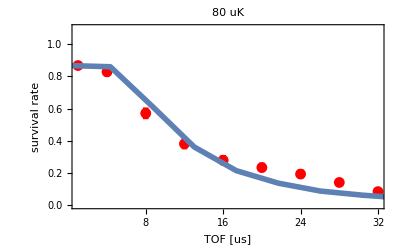

```mathematica
nSim=10000;(*number of random atoms*)


g=9.81;

kB = 1.38 10^-23;
amu=1.66054 10^-27;
T=80 10^-6; (*temp of atom in tweezer*)

Ttr=2 0.6 10^-3;

m=133 amu;

fax=√2 18 10^3;
frad=√2 66 10^3;
tRNR=Range[0,100,5];
scale=Max[survival[[;;,1,2]]]; (*scale the curve for <1 survival rate*)

ωax=2π fax;
ωrad=2π frad;
Utr = kB Ttr;

Δxax=√((kB T)/(3 m ωax^2)); (*I don't know why I need the factor of √3 in these to get agreement*)
Δxrad=√((kB T)/(3 m ωrad^2));
Δv=√((kB T)/(3m));

data=Reap[
Do[
xi1rad=RandomVariate[NormalDistribution[0,Δxrad],nSim];
xi2rad=RandomVariate[NormalDistribution[0,Δxrad],nSim];
xiax=RandomVariate[NormalDistribution[0,Δxax],nSim];

vi1rad=RandomVariate[NormalDistribution[0,Δv],nSim];
vi2rad=RandomVariate[NormalDistribution[0,Δv],nSim];
viax=RandomVariate[NormalDistribution[0,Δv],nSim];
(*
vi1rad=RandomVariate[MaxwellDistribution[Δv],nSim];
vi2rad=RandomVariate[MaxwellDistribution[Δv],nSim];
viax=RandomVariate[MaxwellDistribution[Δv],nSim];

(*vel can be + or -*)
vi1rad=RandomChoice[{1,-1}]#&/@vi1rad;
vi2rad=RandomChoice[{1,-1}]#&/@vi2rad;
viax=RandomChoice[{1,-1}]#&/@viax;
*)
xf1rad=vi1rad Δt;
xf2rad=vi2rad Δt-g Δt^2/2;
xfax=viax Δt;

Δx2=xf2rad-xi2rad; (*change in height*)

e=1/2 m(vi1rad^2+vi2rad^2+viax^2)+1/2 m(ωrad^2(xf1rad^2+xf2rad^2)+ωax^2 xfax^2)+m g Δx2;
surv=Less[#,Utr]&/@e;
survNum=Boole[surv];
Sow[{Δt 10^6,Total[survNum]/Length[survNum]}]
,{Δt,tRNR 10^-6}(*rnr time*)
]
][[2,1]];


Show[{
ErrorListPlot[survival,Joined->False,PlotStyle->{Thickness[.01],Red},Frame->{True,True,False,False},FrameLabel->{"TOF [us]","survival rate"},PlotRange->{All,{0,1.1}},PlotLabel->ToString[10^6 T]<>" uK"],
ListPlot[scale data,Joined->True,AxesLabel->{"time[us]","% surviving"},PlotStyle->Thickness[.01]]

}
]
```

# .6mK trap Cs use analytical model; do FITT!!!!!

```mathematica
Clear["Global`*"]
Needs["ErrorBarPlots`"];
```

```mathematica
survival
```

```mathematica
survival={{{2.,0.967032967032967},ErrorBar[{-0.024371374513921684,0.01421848392624836}]},{{10.,0.9411764705882353},ErrorBar[{-0.031015785868900525,0.0207558679482438}]},{{20.,0.8125},ErrorBar[{-0.04298259953747807,0.03653930056840604}]},{{30.,0.7252747252747253},ErrorBar[{-0.04905090016814739,0.04415362353174024}]},{{40.,0.5543478260869565},ErrorBar[{-0.052128089812590206,0.05095931935910736}]},{{50.,0.5058823529411764},ErrorBar[{-0.053981098077050704,0.053844299171441956}]},{{60.,0.34375},ErrorBar[{-0.04664083821352849,0.04986248769806456}]},{{70.,0.33695652173913043},ErrorBar[{-0.047291772679528166,0.05079808403997704}]},{{80.,0.313953488372093},ErrorBar[{-0.04766396580727389,0.051940897109064854}]},{{90.,0.20454545454545456},ErrorBar[{-0.03956600246216696,0.04620543044990952}]},{{100.,0.20652173913043478},ErrorBar[{-0.038939531101480906,0.0452508915502888}]},{{110.,0.21176470588235294},ErrorBar[{-0.04083177326331741,0.047534919638146406}]},{{120.,0.15384615384615385},ErrorBar[{-0.03404129011246926,0.04156637372450933}]}}
```

{{{2.,0.967033},ErrorBar[{-0.0243714,0.0142185}]},{{10.,0.941176},ErrorBar[{-0.0310158,0.0207559}]},{{20.,0.8125},ErrorBar[{-0.0429826,0.0365393}]},{{30.,0.725275},ErrorBar[{-0.0490509,0.0441536}]},{{40.,0.554348},ErrorBar[{-0.0521281,0.0509593}]},{{50.,0.505882},ErrorBar[{-0.0539811,0.0538443}]},{{60.,0.34375},ErrorBar[{-0.0466408,0.0498625}]},{{70.,0.336957},ErrorBar[{-0.0472918,0.0507981}]},{{80.,0.313953},ErrorBar[{-0.047664,0.0519409}]},{{90.,0.204545},ErrorBar[{-0.039566,0.0462054}]},{{100.,0.206522},ErrorBar[{-0.0389395,0.0452509}]},{{110.,0.211765},ErrorBar[{-0.0408318,0.0475349}]},{{120.,0.153846},ErrorBar[{-0.0340413,0.0415664}]}}

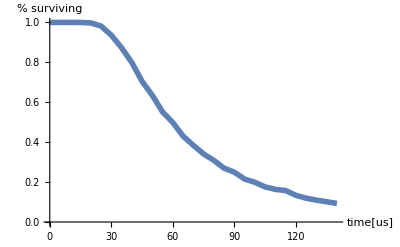

```mathematica
nSim=10000;(*number of random atoms*)


g=9.81;

kB = 1.38 10^-23;
amu=1.66054 10^-27;
T=3.6 10^-6; (*temp of atom in tweezer*)

Ttr=0.7 10^-3;

m=133 amu;

fax=20 10^3;
frad=76 10^3;
tRNR=Range[0,140,5];
scale=Max[survival[[;;,1,2]]]; (*scale the curve for <1 survival rate*)
scale=1;
bkgd=0Min[survival[[;;,1,2]]];
scale=scale-bkgd;
ωax=2π fax;
ωrad=2π frad;
Utr = kB Ttr;

Δxax=√((kB T)/(3 m ωax^2)); (*I don't know why I need the factor of √3 in these to get agreement*)
Δxrad=√((kB T)/(3 m ωrad^2));
Δv=√((kB T)/(3m));

data=Reap[
Do[
xi1rad=RandomVariate[NormalDistribution[0,Δxrad],nSim];
xi2rad=RandomVariate[NormalDistribution[0,Δxrad],nSim];
xiax=RandomVariate[NormalDistribution[0,Δxax],nSim];

vi1rad=RandomVariate[NormalDistribution[0,Δv],nSim];
vi2rad=RandomVariate[NormalDistribution[0,Δv],nSim];
viax=RandomVariate[NormalDistribution[0,Δv],nSim];
(*
vi1rad=RandomVariate[MaxwellDistribution[Δv],nSim];
vi2rad=RandomVariate[MaxwellDistribution[Δv],nSim];
viax=RandomVariate[MaxwellDistribution[Δv],nSim];

(*vel can be + or -*)
vi1rad=RandomChoice[{1,-1}]#&/@vi1rad;
vi2rad=RandomChoice[{1,-1}]#&/@vi2rad;
viax=RandomChoice[{1,-1}]#&/@viax;
*)
xf1rad=vi1rad Δt;
xf2rad=vi2rad Δt-g Δt^2/2;
xfax=viax Δt;

Δx2=xf2rad-xi2rad; (*change in height*)

e=1/2 m(vi1rad^2+vi2rad^2+viax^2)+1/2 m(ωrad^2(xf1rad^2+xf2rad^2)+ωax^2 xfax^2)+m g Δx2;
surv=Less[#,Utr]&/@e;
survNum=Boole[surv];
Sow[{Δt 10^6,Total[survNum]/Length[survNum]}]
,{Δt,tRNR 10^-6}(*rnr time*)
]
][[2,1]];


Show[{(*
ErrorListPlot[survival,Joined->False,PlotStyle->{Thickness[.01],Red},Axes->False,Frame->{True,True,False,False},FrameLabel->{"TOF [us]","survival rate"},PlotRange->{All,{0,1.1}},PlotLabel->ToString[10^6 T]<>" uK"],*)
ListPlot[scale data+bkgd,Joined->True,AxesLabel->{"time[us]","% surviving"},PlotStyle->Thickness[.01]]

}
]
```

```mathematica
"
```